Elizabeth Alejandra Ortiz Durán

# Generador de redes a partir de un libro

```mathematica
(*Función para leer el archivo y regresar el grafico con los pesos de las aristas, como input recibe la ubicacion del archivo y la lista de nombres*)
```

```mathematica
Graficadeunlibro[url_,listanombres_]:=Module[{libro,conteo,pesovertices,posicionestring,inicio,final,stringrecorado,stringlimpio,palabraslimpias,palabraslimpias2,posicionespalabras,ubicacionnombres,nombresorden,diferencia,aristas,grafica,graficalimpia,pesosnom},libro=Import[url,"Plaintext"];conteo=WordCounts[libro];pesovertices=Table[listanombres[[i]]/.conteo,{i,1,Length[listanombres]}];
pesosnom=Thread[listanombres->pesovertices];
posicionestring=Table[StringPosition[libro,listanombres[[i]]],{i,1,Length[listanombres]}];inicio=Flatten[posicionestring]//Min;final=Flatten[posicionestring]//Max;
stringrecorado=StringTake[libro,{inicio,final}];
stringlimpio=StringReplace[stringrecorado,{","-> " ",";"-> " ","."-> " ",":"-> " ","-"-> " ","«"-> " ","»"-> " ","?"-> " ", "¿"-> " ","\""-> " "}];
palabraslimpias=StringSplit[stringlimpio];
palabraslimpias2=Table[StringDelete[palabraslimpias[[i]],".97"],{i,1,Length[palabraslimpias]}];
posicionespalabras=Table[Position[palabraslimpias2,listanombres[[i]]],{i,1,Length[listanombres]}];
ubicacionnombres=Flatten[posicionespalabras];
nombresorden=Sort[ubicacionnombres];
diferencia=Flatten[Table[nombresorden[[i]]-nombresorden[[i-1]],{i,2,Length[nombresorden]}]];
aristas=Table[If[diferencia[[i]]<=15,1,0],{i,1,Length[diferencia]}];
grafica=Table[If[aristas[[i]]==1,palabraslimpias2[[nombresorden[[i]]]]->palabraslimpias2[[nombresorden[[i+1]]]],0],{i,1,Length[aristas]-1}];
graficalimpia=DeleteCases[grafica,0];
{graficalimpia,pesosnom}
]
```

```mathematica
(*Función para generar la imagen del grafico con pesos normalizados en las aristas y en los vertices, como input recibe la red y una asociacion de los vertices (el output de la funcion anterior)*)
```

```mathematica
GraficaVisual[graficalimpia_,pesosvertices_]:=Module[{conteoaristas,aristas2,pesos,nodos,r,vs,styledEdges},conteoaristas=Counts[graficalimpia];aristas2=DeleteDuplicates[graficalimpia];pesos=aristas2/.conteoaristas;nodos=VertexList[graficalimpia];r=nodos/.pesosvertices;
r={r}/Total[r];
vs=Thread[nodos->r[[1]]];
styledEdges=MapThread[Property[#1,EdgeStyle->{Thickness[Min[0.03,#2/40]],Opacity[.5]}]&,{EdgeList[aristas2],Normalize[pesos]}];
Graph[styledEdges,EdgeShapeFunction->{GraphElementData["Arrow","ArrowSize"->0.02]},VertexLabels->Placed["Name",Center],VertexSize->vs,VertexShapeFunction->"Capsule",VertexStyle->Opacity[.7]]]
```

## Red de Pedro Páramo

```mathematica
{grafica,pesosvertices}=Graficadeunlibro["C:\\Users\\rodri\\OneDrive\\Documentos\\Sistemas Complejos\\4. Network 1\\Pedro Paramo.txt",{"Pedro","Susana","Fulgor", "Juan","Rentería","Miguel","Damiana","Justina","Eduviges","Abundio","Dolores","Bartolomé","Donis","Toribio","Fausta","Inocencio"}];
```

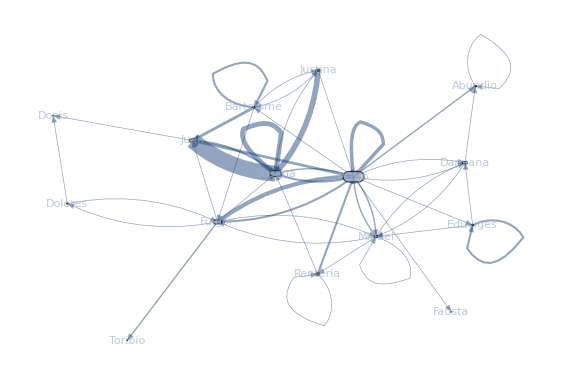

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraficaVisual[%[[1]],%[[2]]]
```

## Red del libro “Aura” por Carlos Fuentes

```mathematica
{graficaaura,pesosvertices}=Graficadeunlibro["C:\\Users\\aleor\\Documents\\Maestria Matematicas\\Dinamica Compleja\\carlos_fuentes_aura.pdf",{"Aura","Felipe","Consuelo"}];
```

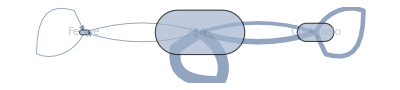

```mathematica
GraficaVisual[%[[1]],%[[2]]]
```

### Tamaño y Densidad

```mathematica
{vertices,aristas}={VertexCount[graficaaura],EdgeCount[graficaaura]}
```

{3,30}

```mathematica
densidad=GraphDensity[graficaaura]
```

2/3

### Longitud Promedio de los caminos mas cortos:

```mathematica
MeanGraphDistance[graficaaura]
```

4/3

### Excentricidad, Diámetro y radio:

```mathematica
Excentricidad=Table[VertexEccentricity[graficaaura,i],{i,{"Aura","Felipe","Consuelo"}}]
```

{1,2,2}

```mathematica
{diametro,radio}={GraphDiameter[graficaaura],GraphRadius[graficaaura]}
```

{2,1}

### Nodos en orden por centralidad de grafo, intermediacion y cercania:

```mathematica
{grado,intermedicion,cercania}={Part[VertexList[graficaaura],Ordering[DegreeCentrality[graficaaura],All,Greater]],Part[VertexList[graficaaura],Ordering[ClosenessCentrality[graficaaura],All,Greater]],Part[VertexList[graficaaura],Ordering[BetweennessCentrality[graficaaura],All,Greater]]}
```

{{Aura,Consuelo,Felipe},{Aura,Consuelo,Felipe},{Aura,Consuelo,Felipe}}

En este caso el orden es siempre el mismo, el nodo mas importante es Aura, el personaje principal.

### Coeficiente de acumulación promedio de la red:

```mathematica
g=DeleteDuplicates[graficaaura]
```

{Felipe->Felipe,Aura->Consuelo,Consuelo->Consuelo,Consuelo->Aura,Aura->Aura,Felipe->Aura,Aura->Felipe}

```mathematica
LocalClusteringCoefficient[g]
```

{0,0,0}

```mathematica
MeanClusteringCoefficient[g]
```

0

```mathematica
GlobalClusteringCoefficient[g]
```

0

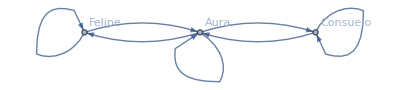

```mathematica
Graph[g,VertexLabels->Automatic]
```

Todos los coeficientes de agrupamiento son cero, esto se debe a que Felipe y Consuelo no son vecinos, por lo tanto los vecinos de cada nodo nunca son vecinos.

### Distribución de grados

```mathematica
VertexDegree[graficaaura]
```

{4,36,20}

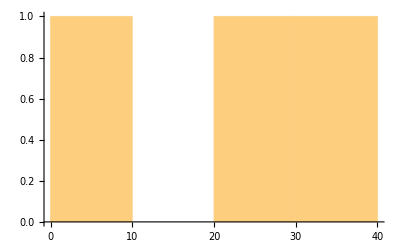

```mathematica
Histogram[VertexDegree[graficaaura],{10}]
```

### Comunidades

El metodo de Louvain esta basado en una optimizacion de la modularidad, en este caso indicamos el metodo con Method→”Modularity”, tambien hay otras opciones como “Centrality”, “CliquePercolation” , ”Hierarchical” y “Spectral”.

```mathematica
FindGraphCommunities[graficaaura,Method->"Modularity"]
```

{{Felipe},{Aura},{Consuelo}}

```mathematica
CommunityGraphPlot[graficaaura,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-

Otra opción para el analisis es quitarle el peso a las aristas:

```mathematica
g=DeleteDuplicates[graficaaura]
```

{Felipe->Felipe,Aura->Consuelo,Consuelo->Consuelo,Consuelo->Aura,Aura->Aura,Felipe->Aura,Aura->Felipe}

```mathematica
CommunityGraphPlot[g,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-

Este análisis tiene un poco mas de sigfnificado ya que en este caso Felipe y Aura estan en la misma comunidad.

## Red de la tragedia “Electra” de Sófocles

```mathematica
Graficadeunlibro["C:\\Users\\aleor\\Documents\\Maestria Matematicas\\Dinamica Compleja\\SOFOCLES - electra.pdf",{"PEDAGOGO","ORESTES","ELECTRA","ARGIVAS","CRISÓTEMIS","CLITEMNESTRA","EGISTO"}];
```

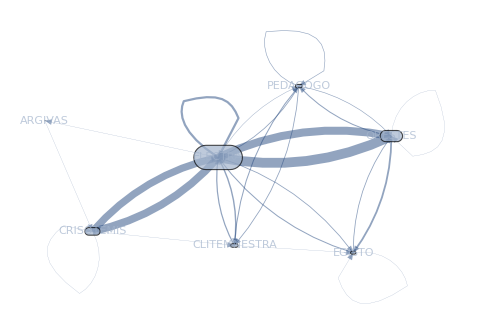

```mathematica
GraficaVisual[%[[1]],%[[2]]]
```

```mathematica
graficaelectra=%[[1]]
```

{ELECTRA->ELECTRA,ELECTRA->PEDAGOGO,PEDAGOGO->ORESTES,ORESTES->ELECTRA,ELECTRA->ARGIVAS,ARGIVAS->CRISÓTEMIS,CRISÓTEMIS->CLITEMNESTRA,CLITEMNESTRA->EGISTO,ELECTRA->PEDAGOGO,ORESTES->PEDAGOGO,ELECTRA->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,PEDAGOGO->PEDAGOGO,CLITEMNESTRA->PEDAGOGO,PEDAGOGO->CLITEMNESTRA,CLITEMNESTRA->PEDAGOGO,PEDAGOGO->ELECTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->PEDAGOGO,PEDAGOGO->ELECTRA,ELECTRA->CLITEMNESTRA,PEDAGOGO->CLITEMNESTRA,PEDAGOGO->CLITEMNESTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->ELECTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->ELECTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->PEDAGOGO,PEDAGOGO->PEDAGOGO,PEDAGOGO->CLITEMNESTRA,CLITEMNESTRA->PEDAGOGO,PEDAGOGO->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,ELECTRA->ELECTRA,CRISÓTEMIS->CRISÓTEMIS,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,CRISÓTEMIS->ELECTRA,ELECTRA->CRISÓTEMIS,ORESTES->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,PEDAGOGO->PEDAGOGO,ORESTES->PEDAGOGO,PEDAGOGO->ORESTES,ORESTES->PEDAGOGO,PEDAGOGO->ORESTES,ORESTES->PEDAGOGO,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ORESTES->PEDAGOGO,PEDAGOGO->ELECTRA,ELECTRA->ELECTRA,CLITEMNESTRA->ELECTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->ELECTRA,CLITEMNESTRA->ELECTRA,ELECTRA->CLITEMNESTRA,CLITEMNESTRA->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,ELECTRA->ORESTES,ELECTRA->ORESTES,ORESTES->ELECTRA,ORESTES->ELECTRA,ELECTRA->ORESTES,ORESTES->ELECTRA,EGISTO->EGISTO,EGISTO->ELECTRA,ELECTRA->EGISTO,EGISTO->ELECTRA,ELECTRA->EGISTO,EGISTO->ELECTRA,ELECTRA->EGISTO,EGISTO->ELECTRA,ELECTRA->EGISTO,ORESTES->EGISTO,ORESTES->EGISTO,EGISTO->ORESTES,ORESTES->EGISTO,EGISTO->ORESTES,ORESTES->EGISTO,ORESTES->EGISTO,EGISTO->ELECTRA,ORESTES->EGISTO,ORESTES->EGISTO,EGISTO->ORESTES,ORESTES->EGISTO,EGISTO->ORESTES,ORESTES->EGISTO}

### Tamaño y Densidad

```mathematica
{vertices,aristas}={VertexCount[graficaelectra],EdgeCount[graficaelectra]}
```

{7,242}

```mathematica
densidad=GraphDensity[graficaelectra]
```

10/21

### Longitud Promedio de los caminos mas cortos:

```mathematica
MeanGraphDistance[graficaelectra]
```

67/42

### Excentricidad, Diámetro y radio:

```mathematica
Excentricidad=Table[VertexEccentricity[graficaelectra,i],{i,{"PEDAGOGO","ORESTES","ELECTRA","ARGIVAS","CRISÓTEMIS","CLITEMNESTRA","EGISTO"}}]
```

{2,2,1,3,2,2,2}

```mathematica
{diametro,radio}={GraphDiameter[graficaelectra],GraphRadius[graficaelectra]}
```

{3,1}

### Nodos en orden por centralidad de grafo, intermediacion y cercania:

```mathematica
{grado,intermedicion,cercania}={Part[VertexList[graficaelectra],Ordering[DegreeCentrality[graficaelectra],All,Greater]],Part[VertexList[graficaelectra],Ordering[ClosenessCentrality[graficaelectra],All,Greater]],Part[VertexList[graficaelectra],Ordering[BetweennessCentrality[graficaelectra],All,Greater]]}
```

{{ELECTRA,CLITEMNESTRA,ORESTES,PEDAGOGO,EGISTO,CRISÓTEMIS,ARGIVAS},{ELECTRA,CLITEMNESTRA,ORESTES,PEDAGOGO,EGISTO,CRISÓTEMIS,ARGIVAS},{ELECTRA,CRISÓTEMIS,CLITEMNESTRA,ORESTES,PEDAGOGO,EGISTO,ARGIVAS}}

```mathematica
g=DeleteDuplicates[graficaelectra];
```

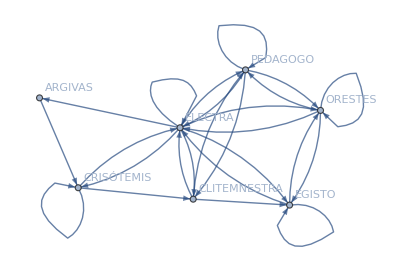

```mathematica
Graph[g,VertexLabels->Automatic]
```

En este caso el nodo mas imporante siempre es Electra, que es el personaje principal, seguido por clitemnestra. En el caso de la centralidad betweeness  vemos como crisotemis toma el segundo lugar, esto se debe a que aunque no es un personaje principal, hay muchos caminos entre nodos que lo atraviesan, osea actua como alguna especie de mensajero.

### Coeficiente de acumulación promedio de la red:

```mathematica
LocalClusteringCoefficient[graficaelectra]
```

{9/25,2/3,2/3,1,2/3,4/7,3/4}

```mathematica
MeanClusteringCoefficient[graficaelectra]
```

3277/4900

```mathematica
GlobalClusteringCoefficient[graficaelectra]
```

27/52

### Distribución de grados

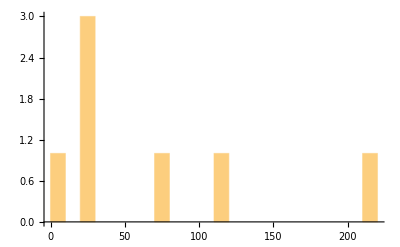

```mathematica
Histogram[VertexDegree[graficaelectra],{10}]
```

### Comunidades

Con pesos en las aristas:

```mathematica
FindGraphCommunities[graficaelectra,Method->"Modularity"]
```

{{ELECTRA,ORESTES,ARGIVAS,CRISÓTEMIS,EGISTO},{PEDAGOGO,CLITEMNESTRA}}

```mathematica
CommunityGraphPlot[graficaelectra,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-

Sin pesos en las aristas:

```mathematica
g=DeleteDuplicates[graficaelectra];
```

```mathematica
CommunityGraphPlot[g,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-

## Red del libro “Orgullo y Prejuicio” de Jane Austen

```mathematica
Graficadeunlibro["C:\\Users\\aleor\\Documents\\Maestria Matematicas\\Dinamica Compleja\\Orgullo y prejuicio.pdf",{"Elizabeth","Darcy","Jane","Mary","Catherine","Lydia","Charles","William","George","Hurst","Charlotte","Georgiana","Bourgh","Anne","Caroline"}];
```

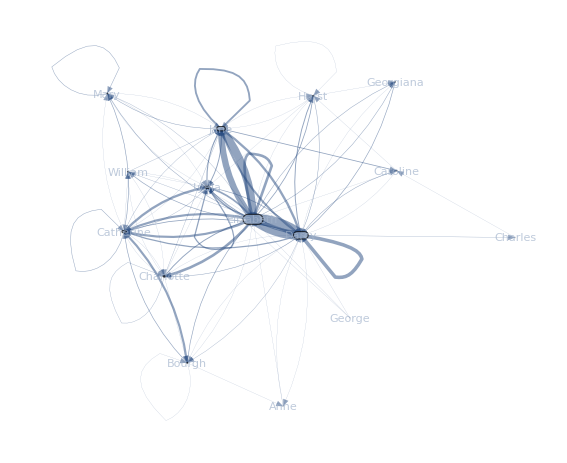

```mathematica
GraficaVisual[%[[1]],%[[2]]]
```

```mathematica
graficao=%[[1]]
```

{Mary->Mary,Hurst->Darcy,Darcy->Hurst,Elizabeth->Darcy,Darcy->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Jane->Mary,Catherine->Lydia,Jane->Elizabeth,Darcy->Darcy,Elizabeth->Darcy,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->William,Darcy->Elizabeth,Catherine->Lydia,Catherine->Lydia,William->Lydia,Jane->Elizabeth,Elizabeth->Jane,Lydia->Elizabeth,Elizabeth->Lydia,Jane->Hurst,Darcy->Hurst,Elizabeth->Jane,Jane->Elizabeth,Darcy->Hurst,Hurst->Elizabeth,Elizabeth->Jane,Hurst->Jane,Darcy->Darcy,Jane->Elizabeth,Darcy->Charles,Charles->Caroline,Caroline->Elizabeth,Elizabeth->Darcy,Elizabeth->Charlotte,Darcy->Elizabeth,Lydia->Jane,Elizabeth->Jane,Jane->Darcy,Darcy->Darcy,Hurst->Hurst,Hurst->Elizabeth,Elizabeth->Darcy,Darcy->Caroline,Darcy->Charles,Darcy->Elizabeth,Darcy->Darcy,Hurst->Elizabeth,Elizabeth->Darcy,Jane->Elizabeth,Elizabeth->Darcy,Hurst->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Hurst,Hurst->Darcy,Darcy->Hurst,Hurst->Darcy,Elizabeth->Elizabeth,Jane->Darcy,Darcy->Elizabeth,Elizabeth->Jane,Jane->Elizabeth,Elizabeth->Mary,Catherine->Lydia,Jane->Elizabeth,Catherine->Bourgh,Bourgh->Bourgh,Catherine->Bourgh,Elizabeth->Catherine,Catherine->Lydia,Catherine->Bourgh,Catherine->Bourgh,Jane->Elizabeth,Elizabeth->Jane,Lydia->Mary,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Jane,Jane->Jane,Elizabeth->Lydia,Lydia->Lydia,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Darcy,Darcy->Darcy,Darcy->Darcy,Catherine->Bourgh,Elizabeth->Bourgh,Bourgh->Catherine,Catherine->Bourgh,Catherine->Bourgh,Bourgh->Anne,Anne->Darcy,Darcy->Darcy,Lydia->Lydia,Elizabeth->Jane,Jane->Jane,Jane->Darcy,Darcy->Catherine,Catherine->Lydia,Elizabeth->Jane,Jane->Elizabeth,Lydia->Elizabeth,Lydia->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Darcy->Darcy,Charlotte->Darcy,Darcy->Charlotte,Elizabeth->Darcy,Elizabeth->Jane,Jane->Darcy,Jane->Elizabeth,Elizabeth->William,George->Darcy,Jane->Elizabeth,Elizabeth->Jane,Bourgh->Catherine,Catherine->Bourgh,Darcy->Elizabeth,Elizabeth->Darcy,Catherine->Bourgh,Bourgh->Darcy,Elizabeth->Mary,Elizabeth->Jane,Mary->Mary,Mary->Elizabeth,Elizabeth->Hurst,Hurst->Lydia,Catherine->Bourgh,Elizabeth->Jane,Jane->Jane,Jane->Elizabeth,Charlotte->Lydia,Elizabeth->Charlotte,Charlotte->Jane,Jane->Elizabeth,Elizabeth->Jane,Jane->Lydia,Jane->Caroline,Jane->Caroline,Jane->Jane,Charlotte->Elizabeth,Charlotte->Charlotte,Elizabeth->Elizabeth,Elizabeth->Elizabeth,Charlotte->Charlotte,William->Jane,Elizabeth->Catherine,Elizabeth->Charlotte,Charlotte->Elizabeth,Jane->Caroline,Jane->Elizabeth,Elizabeth->Jane,Jane->Elizabeth,Darcy->Caroline,Darcy->Elizabeth,Elizabeth->Jane,Caroline->Darcy,Jane->Elizabeth,Elizabeth->Jane,Elizabeth->Darcy,Darcy->Jane,Elizabeth->Jane,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Darcy,Jane->Jane,Darcy->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Jane,Jane->Caroline,Jane->Caroline,Darcy->Darcy,Darcy->Caroline,Caroline->Hurst,Hurst->Elizabeth,Jane->Jane,William->Jane,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Charlotte->William,Catherine->Bourgh,Elizabeth->William,Elizabeth->Jane,Elizabeth->Charlotte,Elizabeth->Charlotte,William->Charlotte,Charlotte->Elizabeth,Elizabeth->Charlotte,Elizabeth->Catherine,Catherine->Bourgh,Elizabeth->Charlotte,Bourgh->Elizabeth,Elizabeth->William,Elizabeth->Catherine,William->Elizabeth,Elizabeth->Catherine,Catherine->Catherine,Elizabeth->Charlotte,Charlotte->Bourgh,Bourgh->Catherine,Elizabeth->Catherine,Catherine->William,Bourgh->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Darcy,Darcy->Bourgh,Bourgh->Catherine,Catherine->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Catherine->Darcy,Georgiana->Darcy,Darcy->Darcy,Catherine->Elizabeth,Elizabeth->Catherine,Catherine->Darcy,Anne->Elizabeth,Elizabeth->Darcy,Bourgh->Elizabeth,Elizabeth->Darcy,Darcy->Catherine,Catherine->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Jane,Darcy->Darcy,Elizabeth->Darcy,Darcy->Jane,Charlotte->Elizabeth,George->Elizabeth,Darcy->Charlotte,Darcy->Charlotte,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Elizabeth->Darcy,Jane->Darcy,Darcy->Darcy,Catherine->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Charlotte->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Darcy,Darcy->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Jane,Jane->Darcy,Jane->Jane,Darcy->Jane,Jane->Elizabeth,Elizabeth->Charlotte,Charlotte->Jane,Jane->Elizabeth,Elizabeth->Catherine,Darcy->Darcy,Darcy->Anne,Elizabeth->Jane,Jane->Catherine,Catherine->Lydia,Jane->Darcy,Elizabeth->Charlotte,Jane->Elizabeth,Elizabeth->Darcy,Catherine->Lydia,Jane->Elizabeth,Elizabeth->Lydia,Mary->Mary,Jane->Mary,Catherine->Lydia,Lydia->Catherine,Mary->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Elizabeth,Darcy->Jane,Elizabeth->Darcy,Jane->Elizabeth,Catherine->Lydia,Catherine->Elizabeth,Catherine->Lydia,Elizabeth->Jane,Jane->Elizabeth,Elizabeth->Lydia,Catherine->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Bourgh->Elizabeth,Catherine->Jane,Elizabeth->Catherine,Darcy->Elizabeth,Darcy->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Georgiana->Darcy,Darcy->Elizabeth,Darcy->Jane,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Hurst,Hurst->Georgiana,Elizabeth->Darcy,Elizabeth->Darcy,Georgiana->Elizabeth,Georgiana->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Georgiana,Elizabeth->Georgiana,Georgiana->Darcy,Darcy->Elizabeth,Elizabeth->Jane,Elizabeth->Jane,Catherine->Lydia,Darcy->Elizabeth,Elizabeth->Lydia,Elizabeth->Darcy,Elizabeth->Jane,Darcy->Elizabeth,Darcy->Elizabeth,Jane->Lydia,Lydia->Jane,Lydia->Lydia,Lydia->Lydia,Jane->Lydia,Lydia->Jane,Jane->Darcy,Elizabeth->Jane,Mary->Catherine,Elizabeth->Jane,Mary->Catherine,Elizabeth->Lydia,Elizabeth->Mary,Elizabeth->Jane,Catherine->Lydia,Lydia->Jane,Jane->Elizabeth,Lydia->Lydia,Lydia->Elizabeth,Catherine->Mary,Elizabeth->Elizabeth,Elizabeth->Elizabeth,Darcy->Lydia,Lydia->Catherine,Jane->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Mary->Catherine,Jane->Lydia,Catherine->Lydia,Lydia->Lydia,Elizabeth->Darcy,Lydia->Darcy,Darcy->Darcy,Lydia->Jane,Jane->Elizabeth,Elizabeth->Jane,Jane->Lydia,Elizabeth->Jane,Jane->Lydia,Lydia->Lydia,Jane->Elizabeth,Elizabeth->Lydia,Lydia->Elizabeth,Elizabeth->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Darcy->Elizabeth,Darcy->Lydia,Lydia->Darcy,Jane->Elizabeth,Elizabeth->Elizabeth,Lydia->Darcy,Lydia->Jane,Elizabeth->Jane,Jane->Darcy,Darcy->Lydia,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Jane->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Jane->Darcy,Jane->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,George->Lydia,Elizabeth->Darcy,Jane->Elizabeth,Darcy->Elizabeth,Darcy->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Catherine,Elizabeth->Catherine,Catherine->Catherine,Catherine->Elizabeth,Catherine->Jane,Jane->Elizabeth,Elizabeth->Elizabeth,Catherine->Elizabeth,Elizabeth->Jane,Jane->Jane,Jane->Jane,Jane->Elizabeth,Jane->Elizabeth,Catherine->Elizabeth,Jane->Elizabeth,Jane->Jane,Lydia->Jane,Jane->Mary,Mary->Catherine,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Catherine->Bourgh,Catherine->Elizabeth,Elizabeth->Elizabeth,Catherine->Elizabeth,Elizabeth->Elizabeth,Charlotte->Catherine,Catherine->Elizabeth,Darcy->Bourgh,Catherine->Elizabeth,Darcy->Catherine,Catherine->Elizabeth,Elizabeth->Catherine,Elizabeth->Darcy,Darcy->Catherine,Catherine->Bourgh,Darcy->Elizabeth,Charlotte->Elizabeth,Catherine->Elizabeth,Darcy->Elizabeth,Elizabeth->Jane,Mary->Jane,Darcy->Catherine,Catherine->Catherine,Catherine->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Catherine,Catherine->Darcy,Elizabeth->Darcy,Catherine->Elizabeth,Elizabeth->Darcy,Darcy->Lydia,Jane->Darcy,Elizabeth->Jane,Darcy->Elizabeth,Darcy->Jane,Jane->Jane,Darcy->Jane,Jane->Elizabeth,Jane->Darcy,Jane->Elizabeth,Elizabeth->Darcy,Darcy->Jane,Darcy->Lydia,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Catherine,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Lydia,Lydia->Darcy,Mary->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Jane->Darcy,Darcy->Catherine,Darcy->Catherine,Jane->Jane,Catherine->Charlotte,Elizabeth->Darcy,Darcy->Darcy,Darcy->William,Darcy->William,Jane->Elizabeth,Elizabeth->Catherine,Darcy->Elizabeth,Elizabeth->Lydia,Darcy->Elizabeth,Lydia->Lydia,Elizabeth->Lydia,Georgiana->Darcy,Darcy->Elizabeth,Elizabeth->Georgiana,Darcy->Georgiana,Georgiana->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Darcy->Elizabeth}

### Tamaño y Densidad

```mathematica
{vertices,aristas}={VertexCount[graficao],EdgeCount[graficao]}
```

{15,566}

```mathematica
densidad=GraphDensity[graficao]
```

11/30

### Longitud Promedio de los caminos mas cortos:

```mathematica
MeanGraphDistance[graficao]
```

∞

Nos da infinito ya que es una red desconexa, el personaje George no esta conectado a ningun otro (no tiene aristas de entrada).

```mathematica
ConnectedComponents[graficao]
```

{{Mary,Hurst,Darcy,Elizabeth,Jane,Catherine,Lydia,William,Charles,Caroline,Charlotte,Bourgh,Anne,Georgiana},{George}}

Si omitimos este personaje tendremos:

```mathematica
Graficadeunlibro["C:\\Users\\aleor\\Documents\\Maestria Matematicas\\Dinamica Compleja\\Orgullo y prejuicio.pdf",{"Elizabeth","Darcy","Jane","Mary","Catherine","Lydia","Charles","William","Hurst","Charlotte","Georgiana","Bourgh","Anne","Caroline"}];
```

```mathematica
graficao2=%[[1]]
```

{Mary->Mary,Hurst->Darcy,Darcy->Hurst,Elizabeth->Darcy,Darcy->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Jane->Mary,Catherine->Lydia,Jane->Elizabeth,Darcy->Darcy,Elizabeth->Darcy,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->William,Darcy->Elizabeth,Catherine->Lydia,Catherine->Lydia,William->Lydia,Jane->Elizabeth,Elizabeth->Jane,Lydia->Elizabeth,Elizabeth->Lydia,Jane->Hurst,Darcy->Hurst,Elizabeth->Jane,Jane->Elizabeth,Darcy->Hurst,Hurst->Elizabeth,Elizabeth->Jane,Hurst->Jane,Darcy->Darcy,Jane->Elizabeth,Darcy->Charles,Charles->Caroline,Caroline->Elizabeth,Elizabeth->Darcy,Elizabeth->Charlotte,Darcy->Elizabeth,Lydia->Jane,Elizabeth->Jane,Jane->Darcy,Darcy->Darcy,Hurst->Hurst,Hurst->Elizabeth,Elizabeth->Darcy,Darcy->Caroline,Darcy->Charles,Darcy->Elizabeth,Darcy->Darcy,Hurst->Elizabeth,Elizabeth->Darcy,Jane->Elizabeth,Elizabeth->Darcy,Hurst->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Hurst,Hurst->Darcy,Darcy->Hurst,Hurst->Darcy,Elizabeth->Elizabeth,Jane->Darcy,Darcy->Elizabeth,Elizabeth->Jane,Jane->Elizabeth,Elizabeth->Mary,Catherine->Lydia,Jane->Elizabeth,Catherine->Bourgh,Bourgh->Bourgh,Catherine->Bourgh,Elizabeth->Catherine,Catherine->Lydia,Catherine->Bourgh,Catherine->Bourgh,Jane->Elizabeth,Elizabeth->Jane,Lydia->Mary,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Jane,Jane->Jane,Elizabeth->Lydia,Lydia->Lydia,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Darcy,Darcy->Darcy,Darcy->Darcy,Catherine->Bourgh,Elizabeth->Bourgh,Bourgh->Catherine,Catherine->Bourgh,Catherine->Bourgh,Bourgh->Anne,Anne->Darcy,Darcy->Darcy,Lydia->Lydia,Elizabeth->Jane,Jane->Jane,Jane->Darcy,Darcy->Catherine,Catherine->Lydia,Elizabeth->Jane,Jane->Elizabeth,Lydia->Elizabeth,Lydia->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Darcy->Darcy,Charlotte->Darcy,Darcy->Charlotte,Elizabeth->Darcy,Elizabeth->Jane,Jane->Darcy,Jane->Elizabeth,Elizabeth->William,Jane->Elizabeth,Elizabeth->Jane,Bourgh->Catherine,Catherine->Bourgh,Darcy->Elizabeth,Elizabeth->Darcy,Catherine->Bourgh,Bourgh->Darcy,Elizabeth->Mary,Elizabeth->Jane,Mary->Mary,Mary->Elizabeth,Elizabeth->Hurst,Hurst->Lydia,Catherine->Bourgh,Elizabeth->Jane,Jane->Jane,Jane->Elizabeth,Charlotte->Lydia,Elizabeth->Charlotte,Charlotte->Jane,Jane->Elizabeth,Elizabeth->Jane,Jane->Lydia,Jane->Caroline,Jane->Caroline,Jane->Jane,Charlotte->Elizabeth,Charlotte->Charlotte,Elizabeth->Elizabeth,Elizabeth->Elizabeth,Charlotte->Charlotte,William->Jane,Elizabeth->Catherine,Elizabeth->Charlotte,Charlotte->Elizabeth,Jane->Caroline,Jane->Elizabeth,Elizabeth->Jane,Jane->Elizabeth,Darcy->Caroline,Darcy->Elizabeth,Elizabeth->Jane,Caroline->Darcy,Jane->Elizabeth,Elizabeth->Jane,Elizabeth->Darcy,Darcy->Jane,Elizabeth->Jane,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Darcy,Jane->Jane,Darcy->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Jane,Jane->Caroline,Jane->Caroline,Darcy->Darcy,Darcy->Caroline,Caroline->Hurst,Hurst->Elizabeth,Jane->Jane,William->Jane,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Charlotte->William,Catherine->Bourgh,Elizabeth->William,Elizabeth->Jane,Elizabeth->Charlotte,Elizabeth->Charlotte,William->Charlotte,Charlotte->Elizabeth,Elizabeth->Charlotte,Elizabeth->Catherine,Catherine->Bourgh,Elizabeth->Charlotte,Bourgh->Elizabeth,Elizabeth->William,Elizabeth->Catherine,William->Elizabeth,Elizabeth->Catherine,Catherine->Catherine,Elizabeth->Charlotte,Charlotte->Bourgh,Bourgh->Catherine,Elizabeth->Catherine,Catherine->William,Bourgh->Elizabeth,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Charlotte,Elizabeth->Darcy,Darcy->Bourgh,Bourgh->Catherine,Catherine->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Catherine->Darcy,Georgiana->Darcy,Darcy->Darcy,Catherine->Elizabeth,Elizabeth->Catherine,Catherine->Darcy,Anne->Elizabeth,Elizabeth->Darcy,Bourgh->Elizabeth,Elizabeth->Darcy,Darcy->Catherine,Catherine->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Jane,Darcy->Darcy,Elizabeth->Darcy,Darcy->Jane,Charlotte->Elizabeth,Darcy->Charlotte,Darcy->Charlotte,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Elizabeth->Darcy,Jane->Darcy,Darcy->Darcy,Catherine->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Charlotte->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Darcy,Darcy->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Darcy->Jane,Jane->Darcy,Jane->Jane,Darcy->Jane,Jane->Elizabeth,Elizabeth->Charlotte,Charlotte->Jane,Jane->Elizabeth,Elizabeth->Catherine,Darcy->Darcy,Darcy->Anne,Elizabeth->Jane,Jane->Catherine,Catherine->Lydia,Jane->Darcy,Elizabeth->Charlotte,Jane->Elizabeth,Elizabeth->Darcy,Catherine->Lydia,Jane->Elizabeth,Elizabeth->Lydia,Mary->Mary,Jane->Mary,Catherine->Lydia,Lydia->Catherine,Mary->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Elizabeth,Darcy->Jane,Elizabeth->Darcy,Jane->Elizabeth,Catherine->Lydia,Catherine->Elizabeth,Catherine->Lydia,Elizabeth->Jane,Jane->Elizabeth,Elizabeth->Lydia,Catherine->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Bourgh->Elizabeth,Catherine->Jane,Elizabeth->Catherine,Darcy->Elizabeth,Darcy->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Georgiana->Darcy,Darcy->Elizabeth,Darcy->Jane,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Hurst,Hurst->Georgiana,Elizabeth->Darcy,Elizabeth->Darcy,Georgiana->Elizabeth,Georgiana->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Elizabeth->Georgiana,Elizabeth->Georgiana,Georgiana->Darcy,Darcy->Elizabeth,Elizabeth->Jane,Elizabeth->Jane,Catherine->Lydia,Darcy->Elizabeth,Elizabeth->Lydia,Elizabeth->Darcy,Elizabeth->Jane,Darcy->Elizabeth,Darcy->Elizabeth,Jane->Lydia,Lydia->Jane,Lydia->Lydia,Lydia->Lydia,Jane->Lydia,Lydia->Jane,Jane->Darcy,Elizabeth->Jane,Mary->Catherine,Elizabeth->Jane,Mary->Catherine,Elizabeth->Lydia,Elizabeth->Mary,Elizabeth->Jane,Catherine->Lydia,Lydia->Jane,Jane->Elizabeth,Lydia->Lydia,Lydia->Elizabeth,Catherine->Mary,Elizabeth->Elizabeth,Elizabeth->Elizabeth,Darcy->Lydia,Lydia->Catherine,Jane->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Mary->Catherine,Jane->Lydia,Catherine->Lydia,Lydia->Lydia,Elizabeth->Darcy,Lydia->Darcy,Darcy->Darcy,Lydia->Jane,Jane->Elizabeth,Elizabeth->Jane,Jane->Lydia,Elizabeth->Jane,Jane->Lydia,Lydia->Lydia,Jane->Elizabeth,Elizabeth->Lydia,Lydia->Elizabeth,Elizabeth->Lydia,Lydia->Elizabeth,Lydia->Elizabeth,Darcy->Elizabeth,Darcy->Lydia,Lydia->Darcy,Jane->Elizabeth,Elizabeth->Elizabeth,Lydia->Darcy,Lydia->Jane,Elizabeth->Jane,Jane->Darcy,Darcy->Lydia,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Jane->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Jane->Darcy,Darcy->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Jane->Darcy,Jane->Elizabeth,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Jane->Elizabeth,Darcy->Elizabeth,Darcy->Elizabeth,Jane->Elizabeth,Jane->Elizabeth,Elizabeth->Catherine,Elizabeth->Catherine,Catherine->Catherine,Catherine->Elizabeth,Catherine->Jane,Jane->Elizabeth,Elizabeth->Elizabeth,Catherine->Elizabeth,Elizabeth->Jane,Jane->Jane,Jane->Jane,Jane->Elizabeth,Jane->Elizabeth,Catherine->Elizabeth,Jane->Elizabeth,Jane->Jane,Lydia->Jane,Jane->Mary,Mary->Catherine,Jane->Elizabeth,Elizabeth->Jane,Darcy->Jane,Catherine->Bourgh,Catherine->Elizabeth,Elizabeth->Elizabeth,Catherine->Elizabeth,Elizabeth->Elizabeth,Charlotte->Catherine,Catherine->Elizabeth,Darcy->Bourgh,Catherine->Elizabeth,Darcy->Catherine,Catherine->Elizabeth,Elizabeth->Catherine,Elizabeth->Darcy,Darcy->Catherine,Catherine->Bourgh,Darcy->Elizabeth,Charlotte->Elizabeth,Catherine->Elizabeth,Darcy->Elizabeth,Elizabeth->Jane,Mary->Jane,Darcy->Catherine,Catherine->Catherine,Catherine->Darcy,Darcy->Elizabeth,Elizabeth->Darcy,Darcy->Catherine,Catherine->Darcy,Elizabeth->Darcy,Catherine->Elizabeth,Elizabeth->Darcy,Darcy->Lydia,Jane->Darcy,Elizabeth->Jane,Darcy->Elizabeth,Darcy->Jane,Jane->Jane,Darcy->Jane,Jane->Elizabeth,Jane->Darcy,Jane->Elizabeth,Elizabeth->Darcy,Darcy->Jane,Darcy->Lydia,Elizabeth->Darcy,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Elizabeth->Catherine,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Lydia,Lydia->Darcy,Mary->Elizabeth,Elizabeth->Darcy,Elizabeth->Darcy,Darcy->Elizabeth,Jane->Darcy,Darcy->Catherine,Darcy->Catherine,Jane->Jane,Catherine->Charlotte,Elizabeth->Darcy,Darcy->Darcy,Darcy->William,Darcy->William,Jane->Elizabeth,Elizabeth->Catherine,Darcy->Elizabeth,Elizabeth->Lydia,Darcy->Elizabeth,Lydia->Lydia,Elizabeth->Lydia,Georgiana->Darcy,Darcy->Elizabeth,Elizabeth->Georgiana,Darcy->Georgiana,Georgiana->Elizabeth,Elizabeth->Elizabeth,Elizabeth->Darcy,Darcy->Darcy,Darcy->Elizabeth}

```mathematica
MeanGraphDistance[graficao2]
```

303/182

### Excentricidad, Diámetro y radio:

```mathematica
Excentricidad=Table[VertexEccentricity[graficao2,i],{i,{"Elizabeth","Darcy","Jane","Mary","Catherine","Lydia","Charles","William","Hurst","Charlotte","Georgiana","Bourgh","Anne","Caroline"}}]
```

{2,2,2,3,2,2,3,3,2,2,2,2,2,2}

```mathematica
{diametro,radio}={GraphDiameter[graficao2],GraphRadius[graficao2]}
```

{3,2}

### Nodos en orden por centralidad de grafo, intermediacion y cercania:

```mathematica
{grado,intermedicion,cercania}={Part[VertexList[graficao],Ordering[DegreeCentrality[graficao],All,Greater]],Part[VertexList[graficao],Ordering[ClosenessCentrality[graficao],All,Greater]],Part[VertexList[graficao],Ordering[BetweennessCentrality[graficao],All,Greater]]}
```

{{Elizabeth,Darcy,Catherine,Jane,Lydia,Charlotte,Hurst,Bourgh,William,Mary,Caroline,Georgiana,Anne,George,Charles},{Darcy,Elizabeth,Catherine,Charlotte,Jane,Lydia,Hurst,Bourgh,Caroline,George,Georgiana,Anne,William,Mary,Charles},{Darcy,Elizabeth,Caroline,Jane,Catherine,Lydia,Hurst,Bourgh,Charlotte,Georgiana,George,Anne,Charles,William,Mary}}

En este caso el orden varia un poco, pero al final los mas importantes Darcy Y Elizabeth siguen a la cabeza, variando poco pero dejando claro que son los personajes principales, en el caso de la centralidad de intermediacion vemos como “Caroline” actua como una especie de mensajero.

### Coeficiente de acumulación promedio de la red:

```mathematica
LocalClusteringCoefficient[graficao]
```

{1,13/17,41/122,47/120,16/25,33/49,27/40,6/7,1,3/4,19/24,11/13,1,0,1}

```mathematica
MeanClusteringCoefficient[graficao]
```

4251106681/5945121000

```mathematica
GlobalClusteringCoefficient[graficao]
```

29/53

### Distribución de grados

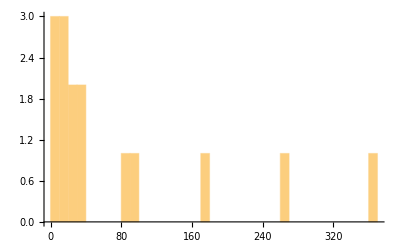

```mathematica
Histogram[VertexDegree[graficao],{10}]
```

### Comunidades

Con peso en las aristas:

```mathematica
FindGraphCommunities[graficao,Method->"Modularity"]
```

{{Hurst,Darcy,Elizabeth,Jane,Charles,Caroline,Georgiana},{Mary,Catherine,Lydia,Bourgh,Anne,George},{William,Charlotte}}

```mathematica
CommunityGraphPlot[graficao,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-

Sin peso en las aristas:

```mathematica
g=DeleteDuplicates[graficao];
```

```mathematica
CommunityGraphPlot[g,Method->"Modularity",VertexLabels->Automatic]
```

-Graphics-